# Derive of SB limit

First, we give the equation of the mean field effective potential (only the thermal part):
U(m^2,β)=2/3 N_f N_c∫(d^3 q)/(2π)^3 q^2/E_q(-n_F(E_q,β,μ)-n_F(E_q,β,-μ))
Integrate the angles
U(m^2,β)=2/3(N_f N_c)/(2 π^2)∫q^2 dq q^2/E_q(-n_F(E_q,β,μ)-n_F(E_q,β,-μ))
=(N_f N_c)/(3 π^2)∫dq q^4/E_q(-n_F(E_q,β,μ)-n_F(E_q,β,-μ))
Then we use the variable substitution q*β -> x, so we have
=(N_f N_c)/(3 π^2 β^4)∫dx x^4/(√(x^2+β^2 m^2))(-1/(e^(√(x^2+β^2 m^2)-μβ))-1/(e^(√(x^2+β^2 m^2)+μβ)))
We can see, when we go to high temperature limit, the β is going to 0, so we have β^2 m^2->0
=(N_f N_c)/(3 π^2 β^4)∫dx x^4/(√(x^2))(-1/(e^(√(x^2)-μβ))-1/(e^(√(x^2)+μβ)))
Then we expand this equation around β=0
=(N_f N_c)/β^4[(7 π^2)/180+1/6(μβ)^2+1/(12 π^2)(μβ)^4+...]
This is the form of SB-limit.

```mathematica
Integrate[x^4/(√(x^2))*(1/(Exp[√(x^2)-μ β]+1)+1/(Exp[√(x^2)+μ β]+1)),{x,0,∞},Assumptions->{μ>0}]
```

-6 (PolyLog[4,-ⅇ^(-β μ)]+PolyLog[4,-ⅇ^(β μ)])

```mathematica
Series[ (PolyLog[4,-ⅇ^(-β μ)]+PolyLog[4,-ⅇ^(β μ)]),{β,0,4}]
```

-(7 π^4)/360-1/12 (π^2 μ^2) β^2-(μ^4 β^4)/24+O[β]^5

# Derive of High T limit of Z_π

## Full equation

First, we give the equation of the pion wave function renormalization
Z_π=-2 N_c h^2 1/q^3∫(d^3 q)/(2π)^3(-F_2+2 cos^2 θ F_3)
=-2 N_c h^2 1/((2π)^3 q^3)∫q^2 dq∫dcosθ∫dϕ(-F_2+2 cos^2 θ F_3)
=-2 N_c h^2 1/((2π)^3 q)∫dq∫dcosθ∫dϕ(-F_2+2 cos^2 θ F_3)
=-2 N_c h^2 1/((2π)^3 q)∫dq(-4π F_2+2/3 4π F_3)
=-2 N_c h^2 1/(2 π^2)∫dq/q(-F_2+2/3 F_3)
=-2 N_c h^2 v_3∫dq/q(-F_2+2/3 F_3)

## F_2 part

We first deal with the F_2 part of the equation.
∫dq/q F_2=∫dq/q q^3/(4(√(q^2+m^2))^3)(√(q^2+m^2)n_F'[√(q^2+m^2),β,μ]+√(q^2+m^2)n_F'[√(q^2+m^2),β,-μ]-n_F[√(q^2+m^2),β,μ]-n_F[√(q^2+m^2),β,-μ])
=∫dq q^2/(4(√(q^2+m^2))^3)(√(q^2+m^2)n_F'[√(q^2+m^2),β,μ]+√(q^2+m^2)n_F'[√(q^2+m^2),β,-μ]-n_F[√(q^2+m^2),β,μ]-n_F[√(q^2+m^2),β,-μ])
Then we use the variable substitution q*β -> x, so we have
=∫dx x^2/(4(√(x^2+β^2 m^2))^3)((√(x^2+β^2 m^2))/β n_F'[√(x^2+β^2 m^2),β,μ]+(√(x^2+β^2 m^2))/β n_F'[√(x^2+β^2 m^2),β,-μ]-n_F[√(x^2+β^2 m^2),β,μ]-n_F[√(x^2+β^2 m^2),β,-μ])
Then we find out 
=∫dx x^2/(4(√(x^2+β^2 m^2))^3)(-n_F[√(x^2+β^2 m^2),β,μ]-n_F[√(x^2+β^2 m^2),β,-μ])
This part is divergent at infrared side. The other part
=1/β∫dx x^2/(4(√(x^2+β^2 m^2))^3)(√(x^2+β^2 m^2)n_F'[√(x^2+β^2 m^2),β,μ]+√(x^2+β^2 m^2)n_F'[√(x^2+β^2 m^2),β,-μ])
=1/(4β)∫dx (β 1/(e^(x-βμ)+1)(1/(e^(x-βμ)+1)-1)+β 1/(e^(x+βμ)+1)(1/(e^(x+βμ)+1)-1))
=1/(4β)e^βμ β(-2+Cosh(βμ))
Then expand around β=0
=-1/4-1/4 μ/T+1/12(μ/T)^3+O[(μ/T)^4]
So the F_2 part of Z_πis
Z_π(F_2)=-1/2 N_c h^2 v_3[1+μ/T+1/3(μ/T)^3+4 IRdivergentpartF2]

```mathematica
Integrate[2/(Exp[x]+1)(1/(Exp[x]+1)-1),{x,0,∞}]
```

-1

```mathematica
Series[Exp[β μ](-2+Cosh[β μ]),{β,0,4}]
```

-1-μ β+(μ^3 β^3)/3+(μ^4 β^4)/4+O[β]^5

## F_3 part

Then we deal with the F_3part of the equation.
∫dq/q F_3=∫dq/q q^5/(16(q^2+m^2)^(5/2))*((q^2+m^2)*(-n_F''[√(q^2+m^2),β,μ]-n_F''[√(q^2+m^2),β,-μ])+3(√(q^2+m^2)n_F'[√(q^2+m^2),β,μ]+√(q^2+m^2)n_F'[√(q^2+m^2),β,-μ]-n_F[√(x^2+β^2 m^2),β,μ]-n_F[√(x^2+β^2 m^2),β,-μ]))
Then we also have the IR divergent part
IRdivergentpart=∫dq/q(3 q^5)/(16(q^2+m^2)^(5/2))(-n_F[√(x^2+β^2 m^2),β,μ]-n_F[√(x^2+β^2 m^2),β,-μ])
The rest part is
∫dq/q q^5/(16(q^2+m^2)^(5/2))((q^2+m^2)*(-n_F''[√(q^2+m^2),β,μ]-n_F''[√(q^2+m^2),β,-μ])+3(√(q^2+m^2)n_F'[√(q^2+m^2),β,μ]+√(q^2+m^2)n_F'[√(q^2+m^2),β,-μ]))
=∫dx x^4/(16(x^2+β^2 m^2)^(5/2))((x^2+β^2 m^2)/β^2(-n_F''[√(x^2+β^2 m^2),β,μ]-n_F''[√(x^2+β^2 m^2),β,-μ])+3((√(x^2+β^2 m^2))/β n_F'[√(x^2+β^2 m^2),β,μ]+(√(x^2+β^2 m^2))/β n_F'[√(x^2+β^2 m^2),β,-μ]))
=∫dx 1/(16x)(x^2/β^2(-n_F''[√(x^2+β^2 m^2),β,μ]-n_F''[√(x^2+β^2 m^2),β,-μ])+3 x/β(n_F'[√(x^2+β^2 m^2),β,μ]+n_F'[√(x^2+β^2 m^2),β,-μ]))
=1/16∫dx(x/β^2(-n_F''[√(x^2+β^2 m^2),β,μ]-n_F''[√(x^2+β^2 m^2),β,-μ])+3/β(n_F'[√(x^2+β^2 m^2),β,μ]+n_F'[√(x^2+β^2 m^2),β,-μ]))
=1/16∫dx(-x/β^2(n_F[μ](n_F[μ]-1)(2n_F[μ]-1)β^2+n_F[-μ](n_F[-μ]-1)(2n_F[-μ]-1)β^2)+3/β(n_F[μ](n_F[μ]-1)β+n_F[-μ](n_F[-μ]-1)β))
=1/16∫dx(-x(n_F[μ](n_F[μ]-1)(2n_F[μ]-1)+n_F[-μ](n_F[-μ]-1)(2n_F[-μ]-1))+3(n_F[μ](n_F[μ]-1)+n_F[-μ](n_F[-μ]-1)))

```mathematica
Integrate[-2x(1/(Exp[x]+1)(1/(Exp[x]+1)-1)(2/(Exp[x]+1)-1)),{x,0,∞}]
```

-1

```mathematica
Integrate[3(1/(Exp[x]+1)(1/(Exp[x]+1)-1))2,{x,0,∞},Assumptions->{μ>0&&β>0}]
```

-3

Then we have
∫dq/q F_3=1/16(-4+16IRdivergentpart)
Z_π(F_3)=-2 N_c h^2 v_3 2/3 1/16(-4+16IRdivergentpart)
=-1/12 N_c h^2 v_3(-4+16IRdivergentpartF3)

## Full Z_π expansion

Z_π=-1/2 N_c h^2 v_3[1+4 IRdivergentpartF2]-1/12 N_c h^2 v_3[-4+16IRdivergentpartF3]
=-1/2 N_c h^2 v_3[1+4 IRdivergentpartF2]+1/3 N_c h^2 v_3[1-4IRdivergentpartF3]
=-1/6 N_c h^2 v_3+[-2IRdivergentpartF2-4/3 IRdivergentpartF3]N_c h^2 v_3

## IR divergent part

-(2 h^2 N_c)/π^2∫dq[q^2/(4(q^2+m^2)^(3/2))-q^4/(8(q^2+m^2)^(5/2))]n_f(√(q^2+m^2),T)
Then we take High T limit n_f->1/2
-(h^2 N_c)/π^2∫dq[q^2/(4(q^2+m^2)^(3/2))-q^4/(8(q^2+m^2)^(5/2))]
Assume f(q,m)=q^2/(4(q^2+m^2)^(3/2))-q^4/(8(q^2+m^2)^(5/2))

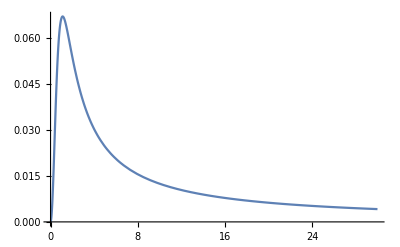

```mathematica
Plot[q^2/(4(q^2+m^2)^(3/2))-q^4/(8(q^2+m^2)^(5/2))/.{m->1},{q,0,30},PlotRange->All]
```

So this term always gives a negative contribution to the equation.
If we expand the distribution function at high temperature limit

```mathematica
Series[1/(Exp[(√(q^2+m^2))/T]+1),{T,∞,2}]
```

1/2-(√(m^2+q^2))/(4 T)+O[1/T]^3

Here we only take the leading order. So we have
-(h^2 N_c)/π^2∫dq[q^2/(4(q^2+m^2)^(3/2))-q^4/(8(q^2+m^2)^(5/2))]
=-(h^2 N_c)/(24 π^2)[(-3 m^2 Λ-2 Λ^3)/((m^2+Λ^2)^(3/2))+(3Log[m^2])/2-3Log[-Λ+√(m^2+Λ^2)]]

```mathematica
Integrate[q^2/(4(q^2+m^2)^(3/2))-q^4/(8(q^2+m^2)^(5/2)),{q,0,Λ},Assumptions->{Λ>m^2>0}]
```

1/24 ((-3 m^2 Λ-2 Λ^3)/((m^2+Λ^2)^(3/2))+(3 Log[m^2])/2-3 Log[-Λ+√(m^2+Λ^2)])

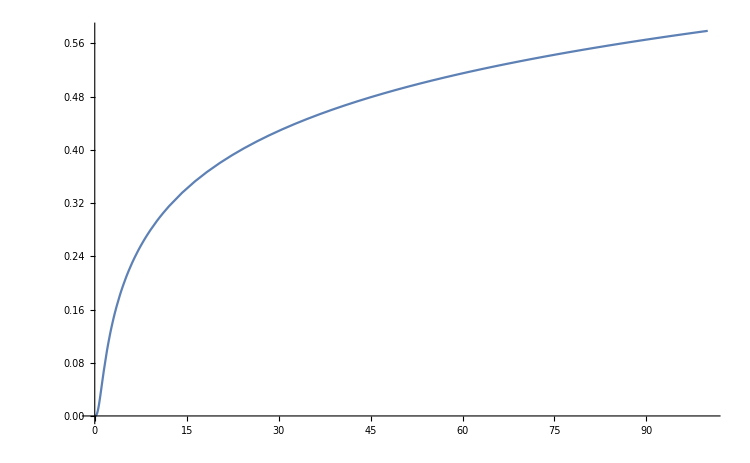

```mathematica
Plot[1/24 ((-3 m^2 Λ-2 Λ^3)/((m^2+Λ^2)^(3/2))+(3 Log[m^2])/2-3 Log[-Λ+√(m^2+Λ^2)])/.{m->1},{Λ,0.001,100}]
```